## Michael Dobbs Musical Rule Characterization & Composition

```mathematica
ClearAll[rule,note,notelist,initset,completenotelist,noteplot,notehist,transpose,retrograde,inversion,retrogradeinversion,shift,scaleshift,palette,durationall,variation,v1,v2,beat,compiler,instruments,run]
```

## 12-Note Rule-Space

```mathematica
(*
The following functions create the n-neighbour 12-scale rule space with 12^(12^n) different rules
n = number of neighbours, m = number of iterations
*)

l = 5;
(*type of scale, i.e. 5 = pentatonic, 12 = chromatic*)

rule[rulenumber_,n_]:=AssociationThread[Tuples[Range[0,l-1],n]->IntegerDigits[rulenumber,l,l^n]];
(*creates a rule based on a rule number and a number of neighbours*)

note[rulenumber_,init_,n_]:=Append[init,
Lookup[rule[rulenumber,n],{Part[init,Length[init]-(n-1);;Length[init]]}][[1]]
];
(*appends the following note to the list based on the rule*)

notelist[rulenumber_,init_,n_,m_]:=Nest[note[rulenumber,#,n]&,init,m];
(*create the sequence of notes to be played*)

initset[n_]:=Tuples[Range[0,l-1],n];
(*Set of all initial conditions*)

completenotelist[rulenumber_,n_,m_]:=Table[notelist[rulenumber,initset[n][[i]],n,m],{i,1,Length[initset[n]]}];
(*combine lists w/ diff. starting conditions*)

noteplot[rulenumber_,n_,m_]:=ListLinePlot[completenotelist[rulenumber,n,m],AxesLabel->{t,Pitch}]
(*visualize the progression of notes*)

notehist[rulenumber_,n_,m_]:=Histogram[completenotelist[rulenumber,n,m],AxesLabel->{Pitch}]
(*represents "amount" of time spent on a note on avg.*)
```

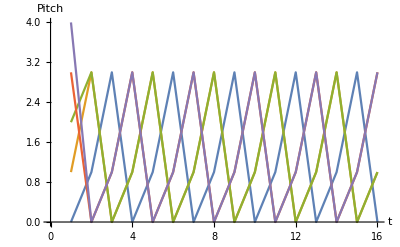

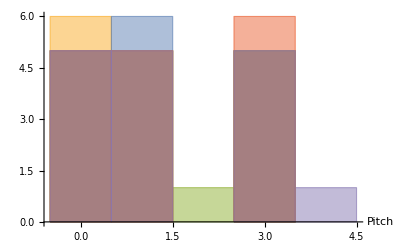

```mathematica
(*some examples*)
noteplot[891610044825,1,3*Length[rule[891610044825,1]]]
notehist[891610044825,1,3*Length[rule[891610044825,1]]]
```

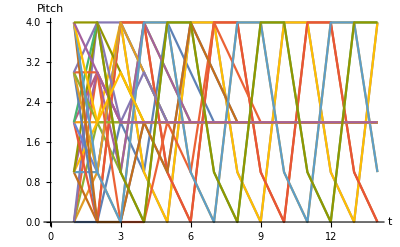

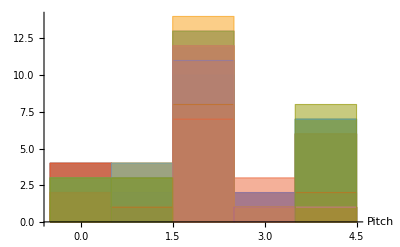

```mathematica
noteplot[12^(12^2)-5000000000000000000000000000,2,12]
notehist[12^(12^2)-5000000000000000000000000000,2,12]
```

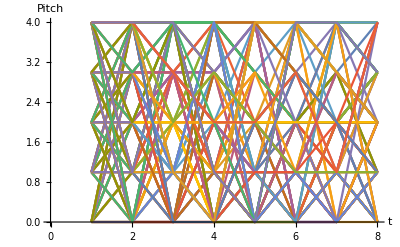

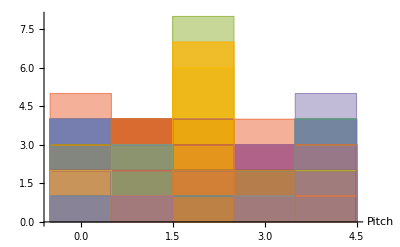

```mathematica
noteplot[12^(12^2),3,5]
notehist[12^(12^2),3,5]
```

## Palette of Variations

```mathematica
(*The following functions replicate compositional techniques that composers use to create music*)

(*
   m = pitch classes available to randomize, related to f of sound by: (p = 9 + 12 * Log[f / 440, 2])
	0 = middle C
	C C# D D# E F F# G G# A A# B then back to C 
tempo = integer (bpm)
*)

transpose[m_]:=With[
{t=Table[Table[m[[i]]+j,{i,1,Length[m]}],{j,1,11}]},
Prepend[t,m]
]; 
(*This double table function shows up in several of the following functions. Its function is to tranpose the motive into all twelve starting notes*)

inv[m_]:=With[
{t=Table[m[[i]]-m[[i+1]],{i,1,Length[m]-1}]},
Prepend[t,m[[1]]]
];
(*This table function shows up in several of the following functions. It's function is to invert the notes*)

shift[m_]:=With[
{s=Table[m[[i]]+1,{i,1,Length[m]-1}]},
Prepend[s,m[[1]]]
];
(*This table function shows up in scaleshift*)

div[m_]:=With[
{d=Union[m,Table[Round[(m[[i]]+m[[i+1]])/2],{i,1,Length[m]-1}]]},
Prepend[d,m]
];

(*
------------------------------------------------------------------------------------------------------------------------------------------------------------------
BASIS FUNCTIONS *)

retrograde[m_]:=With[
{r=Reverse[m]},
transpose[r]
]; 
(*This function simply reverses the note order*)

inversion[m_]:=With[
{in=inv[m]},
transpose[in]
];
(*This function inverts each indivual relationship between the note. For example: A,B will become A,G*)

scaleshift[m_]:=With[
{ss=shift[m]},
transpose[ss]
];
(*This function converts a set of notes a semitone higher*)

dimunition[m_]:=With[
{dim=div[m]},
transpose[dim]
];
(*divides a long note into a series of shorter notes*)

(*
------------------------------------------------------------------------------------------------------------------------------------------------------------------
COMPOSITE FUNCTIONS *)

retrogradeinversion[m_]:=With[
{rt=Reverse[inv[m]]},
transpose[rt]
];
(*This function reverses the inversion*)

retrogradescaleshift[m_]:=With[
{r=Reverse[m]},
s=shift[r];
transpose[s]
]

retrogradedimunition[m_]:=With[
{r=Reverse[m]},
dim=div[r];
transpose[dim]
]

inversionscaleshift[m_]:=With[
{in=inv[m]},
s=shift[in];
transpose[s]
]

inversiondimunition[m_]:=With[
{in=inv[m]},
dim=div[in];
transpose[dim]
]

(*scaleshiftinversion[m_]:=With[
{ss=shift[m]},
in=inv[ss];
transpose[in]
]*)

palette[m_]:={transpose[m],retrograde[m],inversion[m],retrogradeinversion[m],scaleshift[m],dimunition[m],retrogradescaleshift[m],retrogradedimunition[m],inversionscaleshift[m](*,scaleshiftinversion[m]*)};
(*This is the list of variations compiled from all the above functions*)
```

## Making Music

```mathematica
durationall[tempo_,m_]:=(60/tempo)*Length[m]*RandomChoice[{.05,.15,.25,.05,.35,.15,.05}->{4,2,1,2/3,1/2,1/3,1/4}];
(*Determines the note value and duration of each variation*)

variation[i_,tempo_,voice_,m_,d_]:=Sound[
SoundNote[#,1,voice]& /@palette[m][[RandomInteger[{1,9}]]][[RandomInteger[{1,12}]]],
{i,i+d[tempo,m(*,speed*)]}
];
(*Selects one variation at random, chooses one of 4 variations in palette, then 1 of 12 starting notes from scale*)

(*Voice 1*)
v1[m_,voice_,tempo_,d_,l_]:=Sound[
Table[
If[
RandomChoice[{.6,.4}->{variation,rest}]==variation,
variation[i,tempo,voice,m,d],
Nothing,Nothing],
{i,0,l,(60/tempo)}]];
(*Randomly selects to play or to rest and then compiles all of the randomly selected variations into one output*)

(*Voice 2*)
v2[m_,voice2_,tempo_,d_,l_]:=Sound[
Table[
If[
RandomChoice[{.2,.8}->{variation,rest}]==variation,
variation[i,tempo,voice2,m,d],
Nothing,Nothing],
{i,0,l,(60/tempo)}]];
(*Randomly selects to play or to rest and then compiles all of the randomly selected variations into one output*)

compiler[m_,tempo_,l_,voice_,d1_,vol1_,voice2_,d2_,vol2_]:=Sound[{
Sound[v1[m,voice,tempo,d1,l],{0,QuantityMagnitude[Duration[v1[m,voice,tempo,d1,l]]]},SoundVolume->vol1],
Sound[v2[m,voice2,tempo,d2,l],{0,QuantityMagnitude[Duration[v2[m,voice2,tempo,d2,l]]]},SoundVolume->vol2]
}];
(*compiles the two voices together*)

(* NOT IMPLEMENTED YET *)

beat[tempo_]:=Sound[{Table[Sound[SoundNote["C",1,"Woodblock"],{i,i+1}],{i,0,30,(60/tempo)}]}];
(*Used for testing if the composition is following a beat*)
```

## Interface

```mathematica
instruments={"Accordion","AltoSax","Atmosphere","Bagpipe","BassAndLead","Bassoon","Bird","BlownBottle","Bowed","BrassSection","Brightness","Celesta","Cello","Choir","Clarinet","Dulcimer","ElectricGuitar","Fiddle","Fifths","Flute","FrenchHorn","Glockenspiel","Guitar","Harmonica","Harp","Harpsichord","Koto","Marimba","MusicBox","MutedTrumpet","Oboe","OrchestraHit","Organ","PanFlute","Piano","PizzicatoStrings","Recorder","Shamisen","Shanai","Sitar","Strings","TremoloStrings","Trumpet","TubularBells","Vibraphone","Viola","Violin","Voice","Voice|Aahs","VoiceOohs","Warm","Whistle","Woodblock","Xylophone"};

run:=Panel[
DynamicModule[{m={0,4,7},tempo=100,voice1="Piano",voice2="Violin",l=30,vol1=1,vol2=0(*,speed=4*)},
Deploy[
Panel[
Grid[
Transpose[
{{"Pitch Class {}","Tempo (bpm)",(*"Speed of Notes",*)"Length (sec)","Voice 1, Vol.","Voice 2, Vol.",Space},
{InputField[Dynamic[m]],InputField[Dynamic[tempo]],(*SetterBar[Dynamic[speed],{1->"Slow",2->"Medium",3->"Fast",4->"All"}],*)InputField[Dynamic[l]],PopupMenu[Dynamic[voice1],instruments],PopupMenu[Dynamic[voice2],instruments],
Button["Generate",
{(* prints preset variables *)
Print[ToString[voice1]<>","<>ToString[voice2]<>", "<>ToString[tempo]<>"bmp, on "<>ToString[m]<>", for "<>ToString[l]<>"+s."],
(* "prints" music to be played *)
Print[compiler[m,tempo,l,voice1,durationall,vol1,voice2,durationall,vol2]]
}
]
},{Space,Space,Space,Slider[Dynamic[vol1],{0,1},ImageSize->Tiny],Slider[Dynamic[vol2],{0,1},ImageSize->Tiny],Space}}
],
Alignment->Left
],Style["Algorithmic Composer",Italic,24],ImageMargins->10
]
]
]
]
```

```mathematica
run
```